## Euler Number Visibility

Foi testado sem usar as diferencas

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
series=RealDigits[E,10,10000][[1,2;;]];
```

## SDL Complexity

```mathematica
<<sdl.mx
```

```mathematica
result=sdl[series]
```

{0.195338,0.948515}

## Visibility

```mathematica
<<visibility.mx
```

```mathematica
links=naturalVisibilityLinks[series];
```

```mathematica
natGraph=Graph[links, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[natGraph]//Mean//N]
```

{0.195338,0.948515,4.93169}

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|2→1976,5→1162,14→67,3→2103,7→624,4→1608,11→173,9→364,6→835,10→258,17→31,8→486,19→10,13→91,12→118,15→43,16→26,18→13,20→5,24→1,21→1,23→2,22→2|>

```mathematica
If[count[1]<3,count[1]=.];
```

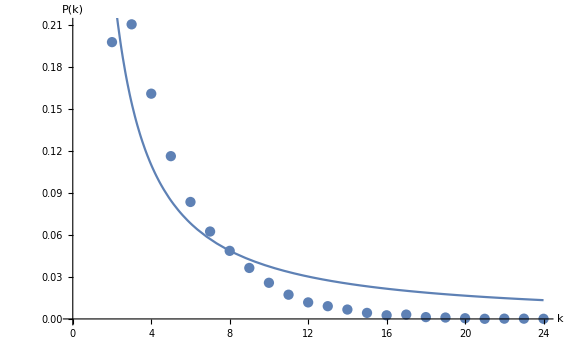
{{{0.5605,0.186777},{1.17488,0.261695}},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

{0.195338,0.948515,4.93169,{{0.5605,0.186777},{1.17488,0.261695}}}

## Horizontal Visibility

```mathematica
horlinks=horizontalVisibilityLinks[series];
```

```mathematica
hg=Graph[horlinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[hg]//Mean//N]
```

{0.195338,0.948515,4.93169,{{0.5605,0.186777},{1.17488,0.261695}},3.41134}

```mathematica
count=VertexDegree[hg]//Counts
```

<|2→3874,4→1553,5→1026,3→2377,8→131,6→630,7→321,9→63,10→19,11→3,12→2|>

```mathematica
If[count[1]<3,count[1]=.];
```

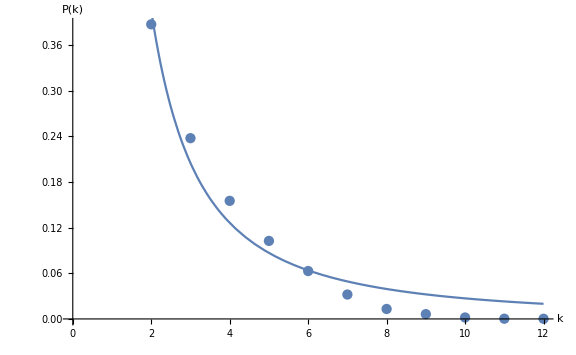
{{{1.30162,0.413578},{1.68238,0.329887}},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

{0.195338,0.948515,4.93169,{{0.5605,0.186777},{1.17488,0.261695}},3.41134,{{1.30162,0.413578},{1.68238,0.329887}}}